```mathematica
U[u_]:=a u^2-b u^3+ c u^4;
```

```mathematica
Integrate[Exp[-U[u] /kT],{u,-Infinity,Infinity}]
```

∫_(-∞)^∞ ⅇ^((-a u^2+b u^3-c u^4)/kT)ⅆu

```mathematica
a=1;b=0.5;c=0.04;Plot[U[u],{u,-10,10},PlotRange->{-5,5}]
a=.;b=.;c=.;
```

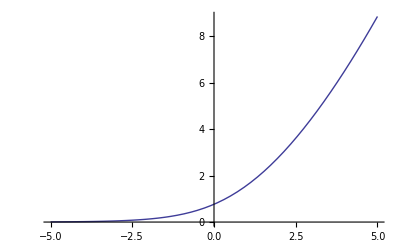

```mathematica
Plot[{},{u,-5,5},PlotRange->All]
```

```mathematica
FindRoot[-PolyLog[3/2,-Exp[u]]==4,{u,0}][[1,2]]
```

2.72977

```mathematica
cf=Compile[{{x,_Real}},FindRoot[]
```

CompiledFunction[{x},FindRoot[u/.FindRoot[-PolyLog[3/2,-ⅇ^u]==n,{u,0}],{u,0}],-CompiledCode-]

```mathematica
f[e_,n_,kT_]:=1/(Exp[(e-FindRoot[-PolyLog[3/2,-Exp[u]]==n,{u,0}][[1,2]])/kT]+1)
```

```mathematica
f[4,0.3,4]
```

0.218473

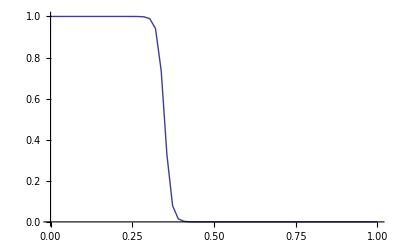

```mathematica
kT=0.001;Plot[f[e,1,kT],{e,0,1 },PlotPoints->8,PerformanceGoal->"Speed",PlotRange->All]
kT=.
```

```mathematica
,
```

```mathematica
-PolyLog[3/2,-Exp[0]]//N
PolyLog[3/2,Exp[0]]//N
```

0.765147

2.61238

PolyLog[3/2,ⅇ]

```mathematica
<<PhysicalConstants`
```

BoltzmannConstant::shdw: Symbol "BoltzmannConstant" appears in multiple contexts {"PhysicalConstants`", "Global`"}; definitions in context "PhysicalConstants`" may shadow or be shadowed by other definitions.

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin